# Points inside a circle

## 2 - D Space

```mathematica
A[r_]:=Table[ 
Table[
If[√(i^2+j^2)≤r,a=a+1,a=a]
,{j,-Floor[r],Floor[r]}]
,{i,-Floor[r],Floor[r]}]
```

```mathematica
NuA[r_]:={a=0, A[r],a}[[3]];
```

```mathematica
NuA[0]
```

1

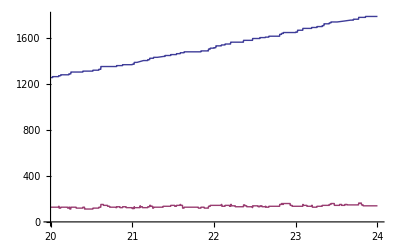

```mathematica
Plot[{NuA[r],-NuA[r-1]+NuA[r]},{r,20,24}]
```

## 3 - D Sphere

```mathematica
B[r_]:=Table[Table[ 
Table[
If[√(i^2+j^2+k^2)≤r,a=a+1,a=a]
,{j,-Floor[r],Floor[r]}]
,{i,-Floor[r],Floor[r]}],
{k,-Floor[r],Floor[r]}]
```

```mathematica
NuB[r_]:={a=0, B[r],a}[[3]];
```

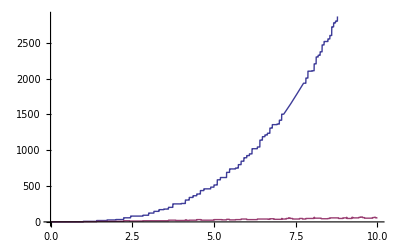

```mathematica
Plot[{NuB[r],-NuA[r-1]+NuA[r]},{r,0,10}]
```